# LTE -Advanced Radiative Transfer Modelling

In this section we will apply the LTE`package to some real astronomical modelling cases.

LTERadiationTemperature[T,ν,fwhm] | T_R=h/k fwhm ν(Exp[(h ν)/(k T)]-1)^-1
LTEBrightnessTemperature[…,"OpticalDepth"→τ] | T_b=T_R(T)(1-exp(-τ))+T_R(T)exp(-τ) 
LTEBrightnessTemperature[…,"OpticalDepth"→τ,"BeamSwitchedObservation"→True] | T_b=(T_R(T)-T_R(2.73))(1-exp(-τ))

Various definitions of the brightness temperature functions.

Simplest Case: homogeneous cloud with no foreground and unity beam coupling

```mathematica
Manipulate[Plot[LTEBrightnessTemperature[{"CO",i},{t,10^col,f}],{f,-3,3},PlotRange->Automatic,PlotTheme->"Scientific"],{{i,1,"Transitions"},Range[20]},{{t,10,"Temperature (K)"},3,300},{{col,16,"Log_10(N_CO)"},12,20}]
```

## Simple Emission

Blue (warm) cloud emitting.

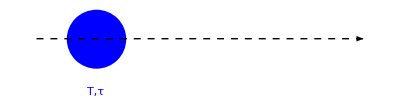

```mathematica
fig1=Graphics[{Blue,Disk[{0,0},1],Text["T_1,τ_1", {0,-1.8}],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}]
```

Consider a cloud of gas emitting radiation at a certain frequency ν. The cloud be homogeneous with temperature T_1 and an optical depth of τ_1. Neglecting any radiating contributing from the background, the total emission is:

T_b=(h ν)/k Δν 1/(exp((h ν)/(k  T_1))-1)×(1-exp[-τ_1])

The first term is the Rayleigh-Jeans radiation temperature of an optically thin black body, the term (1-Exp[-τ_1]) covers the optical thickness effects of a cloud with optical depth τ_1 where the radiation is emitted and absorbed along the line of sight.

## Simple Absorption

Blue cloud absorbing a background.

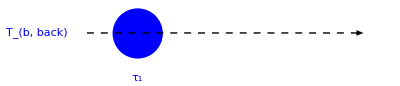

```mathematica
fig1=Graphics[{Blue,Disk[{0,0},1],Text["τ_1", {0,-1.8}],Text["T_(b, back)", {-4,0}],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}]
```

Consider a cloud of gas ab absorbing background radiation T_(b,back) at a certain frequency ν. The cloud is homogeneous with an optical depth of τ_1. Neglecting any radiating contributing from the cloud itself, the total observed emission is:

T_b=T_(b,back)×exp[-τ_1]

The background radiation is attenuated with the term Exp[-τ_1].

## Absorption and Emission

Blue (warm) cloud emitting and absorbing including a background component.

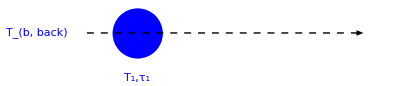

```mathematica
fig1=Graphics[{Blue,Disk[{0,0},1],Text["T_1,τ_1", {0,-1.8}],Text["T_(b, back)", {-4,0}],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}]
```

Consider a cloud of gas ab absorbing background radiation T_(b,back) at a certain frequency ν. The cloud is homogeneous with temperature T_1 and an optical depth of τ_1. The total observed emission is:

T_b=T_(b,back)×exp[-τ_1]+(h ν)/k Δν 1/(exp((h ν)/(k  T_1))-1)×(1-exp[-τ_1])

The first term computes how the background radiation is attenuated with the term Exp[-τ_1]. The second term adds the emission and partial self-absorption of the radiation from the cloud itself.

## Self Absorption

A common case in studies of the interstellar medium is foreground absorption, i.e. radiation emitted by hot gas passes through a colder foreground cloud on its way to the observer:

Blue (warm) cloud with a green (cool) foreground component.

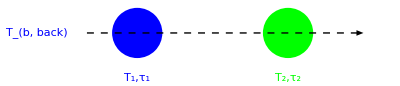

```mathematica
fig2=Graphics[{Blue,Disk[{0,0},1],Text["T_1,τ_1", {0,-1.8}],Text["T_(b, back)", {-4,0}],Green,Disk[{6,0},1],Text["T_2,τ_2", {6,-1.8}],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}]
```

The total observed emission is:

T_b=T_(b,back)×exp[-τ_1]exp[-τ_2]+(h ν)/k Δν 1/(exp((h ν)/(k  T_1))-1)×(1-exp[-τ_1])exp[-τ_2]+(h ν)/k Δν 1/(exp((h ν)/(k  T_2))-1)×(1-exp[-τ_2])-T_(b,back)

The first term covers absorption of the CMB background by both clouds according to exp[-τ_1]exp[-τ_2]. The second term computes how radiation is emitted and absorbed in the blue cloud and absorbed in the green one: (1-exp[-τ_1])exp[-τ_2]. The third term covers the green clouds radiation: ×(1-exp[-τ_2]). The last term subtracts the unabsorbed CMB background, because we perform beam-switched observations.

The temperature difference is crucial here because a cool foreground means, that the molecules in the foreground cloud are less excited (and its levels less populated) than in the emitting cloud. Therefore, molecules in the foreground are able to absorb the photons from the background because the lower energy level is more populated. This leads to self-absorption:

General 2 component setup for CO emission/absorption

```mathematica
h=6.62607*10^-27;
k=1.38065*10^-16;
tMainBeamLTE2Component[v_,{v0b_,Δvb_,τ0b_,Tb_},{v0f_,Δvf_,τ0f_,Tf_},jUp_]:=
With[{
τf=τ0f Exp[-(v-v0f)^2/(2.(Δvf/(2 √(2Log[2.])))^2)],τb=τ0b Exp[-(v-v0b)^2/(2.(Δvb/(2 √(2Log[2.])))^2)],
Tback=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k Tb)]-1)^-1,
Tfore=h/k Δvf transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k Tf)]-1)^-1,Tcmb=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k 2.73)]-1)^-1},
Tback(1-Exp[-τb])Exp[-τf]+Tfore(1-Exp[-τf])+Tcmb(Exp[-τb]Exp[-τf]-1)]
```

```mathematica
v0b=0;Δvb=3;τ0b=3;Tb=30;
v0f=0;Δvf=1;τ0f=1;Tf=10;
jUp=3;
Plot[tMainBeamLTE2Component[v,{v0b,Δvb,τ0b,Tb},{v0f,Δvf,τ0f,Tf},jUp],{v,-5,5},PlotTheme->"Scientific",ImageSize->Medium,FrameLabel->{"v (km/s)","T_B (K)"},PlotLabel->Row[{"CO (",jUp,"-",jUp-1,")"}]]
```

-Graphics-

If the foreground would be warmer than the background it would emit instead of absorb:

```mathematica
v0b=0;Δvb=3;τ0b=3;Tb=20;
v0f=0;Δvf=1;τ0f=1;Tf=120;
jUp=3;
Plot[tMainBeamLTE2Component[v,{v0b,Δvb,τ0b,Tb},{v0f,Δvf,τ0f,Tf},jUp],{v,-5,5},PlotTheme->"Scientific",ImageSize->Medium,FrameLabel->{"v (km/s)","T_B (K)"},PlotLabel->Row[{"CO (",jUp,"-",jUp-1,")"}]]
```

-Graphics-

## Even more complex

Example of a more complex setup.

```mathematica
fig3=Graphics[{Blue,Disk[{0,0},1],Red,Disk[{3,0},1],Green,Disk[{6,0},1],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}];
fig2=Graphics[{Blue,Disk[{0,0},1],Green,Disk[{6,0},1],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}]}];
fig2plus1=Graphics[{Blue,Disk[{0,0},1],Red,Disk[{0,2},1],Green,Disk[{4,1},2],Thick, Black, Dashed,Arrowheads[Medium],Arrow[{{-2,0},{9,0}}],Arrow[{{-2,2},{9,2}}]}];
h=6.62607*10^-27;
k=1.38065*10^-16;
cl=2.99792458×10^10;
tMainBeamLTE2Component[v_,{v0b_,Δvb_,τ0b_,Tb_},{v0f_,Δvf_,τ0f_,Tf_},jUp_,B_]:=
With[{τf=τ0f Exp[-(v-v0f)^2/(2.(Δvf/(2 √(2Log[2.])))^2)],τb=τ0b Exp[-(v-v0b)^2/(2.(Δvb/(2 √(2Log[2.])))^2)],
Tback=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k Tb)]-1)^-1,
Tfore=h/k Δvf transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k Tf)]-1)^-1,Tcmb=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k 2.73)]-1)^-1},
Tback(1-Exp[-τb])Exp[-τf]+Tfore(1-Exp[-τf])+Tcmb(Exp[-τb]Exp[-τf]-1)];
tMainBeamLTE1Component[v_,{v0b_,Δvb_,τ0b_,Tb_},jUp_,B_]:=
With[{τb=τ0b Exp[-(v-v0b)^2/(2.(Δvb/(2 √(2Log[2.])))^2)],
Tback=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k Tb)]-1)^-1,
Tcmb=h/k Δvb transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k 2.73)]-1)^-1},
Tback(1-Exp[-τb])+Tcmb(Exp[-τb]-1)]
tMainBeamLTE3Component[v_,{v01_,Δv1_,τ01_,T1_},{v02_,Δv2_,τ02_,T2_},{v03_,Δv3_,τ03_,T3_},jUp_,B_]:=
(* All components line up. Comp 1 travels thropugh 2 and 3, 2 travels through 3*)
With[{τ3=τ03 Exp[-(v-v03)^2/(2.(Δv3/(2 √(2Log[2.])))^2)],τ1=τ01 Exp[-(v-v01)^2/(2.(Δv1/(2 √(2Log[2.])))^2)],τ2=τ02 Exp[-(v-v02)^2/(2.(Δv2/(2 √(2Log[2.])))^2)],
Tr1=h/k Δv1 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T1)]-1)^-1,Tr2=h/k Δv2 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T2)]-1)^-1,Tr3=h/k Δv3 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T3)]-1)^-1,
Tcmb=h/k Δv1 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k 2.73)]-1)^-1},
Tr1(1-Exp[-τ1])Exp[-τ2]Exp[-τ3]+Tr2(1-Exp[-τ2])Exp[-τ3]+Tr3(1-Exp[-τ3])+Tcmb(Exp[-τ1]Exp[-τ2]Exp[-τ3]-1)]
tMainBeamLTE2Plus1Component[v_,{v01_,Δv1_,τ01_,T1_},{v02_,Δv2_,τ02_,T2_},{v03_,Δv3_,τ03_,T3_},jUp_,B_]:=
(* Not all components line up. Comp 1 travels thropugh 3, 2 travels through 3*)
With[{τ3=τ03 Exp[-(v-v03)^2/(2.(Δv3/(2 √(2Log[2.])))^2)],τ1=τ01 Exp[-(v-v01)^2/(2.(Δv1/(2 √(2Log[2.])))^2)],τ2=τ02 Exp[-(v-v02)^2/(2.(Δv2/(2 √(2Log[2.])))^2)],
Tr1=h/k Δv1 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T1)]-1)^-1,Tr2=h/k Δv2 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T2)]-1)^-1,Tr3=h/k Δv3 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k T3)]-1)^-1,
Tcmb=h/k Δv1 transitionFrequency["CO",jUp](Exp[(h transitionFrequency["CO",jUp])/(k 2.73)]-1)^-1},
(Tr1(1-Exp[-τ1])+Tr2(1-Exp[-τ2]))Exp[-τ3]+Tr3(1-Exp[-τ3])+Tcmb(1/2(Exp[-τ1]+Exp[-τ2])Exp[-τ3]-1)]
```

```mathematica
Manipulate[
Plot[{
Switch[model,
comp3,tMainBeamLTE3Component[v,{v01,Δv1,τ1,T1},{v02,Δv2,τ2,T2},{v03,Δv3,τ3,T3},Jup,Subscript[B, 12CO]],
comp2plus1,tMainBeamLTE2Plus1Component[v,{v01,Δv1,τ1,T1},{v02,Δv2,τ2,T2},{v03,Δv3,τ3,T3},Jup,Subscript[B, 12CO]],
comp2,tMainBeamLTE2Component[v,{v01,Δv1,τ1,T1},{v03,Δv3,τ3,T3},Jup,Subscript[B, 12CO]]],
tMainBeamLTE1Component[v,{v01,Δv1,τ1,T1},Jup,Subscript[B, 12CO]],
tMainBeamLTE1Component[v,{v02,Δv2,τ2,T2},Jup,Subscript[B, 12CO]],
tMainBeamLTE1Component[v,{v03,Δv3,τ3,T3},Jup,Subscript[B, 12CO]]},{v,-20,20},PlotRange->All,
ImageSize->500,Frame->True,PerformanceGoal:>"Speed",PlotStyle->{Directive[Thickness[0.0075],Black],Blue,Red,Green}],
Row[{Control@{{model,comp3,"Model configuration"},{comp2->Subscript[fig2, 1],comp3->Subscript[fig3, 2],comp2plus1->fig2plus1},ControlPlacement->Top},Spacer[20],Control@{{Jup,4,"J_up"},1,20,1,Appearance->"Open"}}],
{{T1,50,Style["T_1 [K]",Blue]},3,300,ControlPlacement->Left,Appearance->"Open"},{{τ1,1,Style["τ_1",Blue]},0,20,ControlPlacement->Left,Appearance->"Open"},{{T2,30,Style["T_2 [K]",Red]},3,300,ControlPlacement->Left,Appearance->"Open"},{{τ2,1,Style["τ_2",Red]},0,20,ControlPlacement->Left,Appearance->"Open"},{{T3,10,Style["T_3 [K]",Green]},3,300,ControlPlacement->Left,Appearance->"Open"},{{τ3,.1,Style["τ_3",Green]},0,20,ControlPlacement->Left,Appearance->"Open"},
{{v01,0,Style["v_(0, 1)[km/s]",Blue]},-15,15,ControlPlacement->Right,Appearance->"Open"},{{Δv1,1,Style["Δv_(1, FWHM) [km/s]",Blue]},0.01,20,ControlPlacement->Right,Appearance->"Open"},{{v02,0,Style["v_(0, 2)[km/s]",Red]},-15,15,ControlPlacement->Right,Appearance->"Open"},{{Δv2,1,Style["Δv_(2, FWHM) [km/s]",Red]},0.01,20,ControlPlacement->Right,Appearance->"Open"},{{v03,0,Style["v_(0, 3)[km/s]",Green]},-15,15,ControlPlacement->Right,Appearance->"Open"},{{Δv3,1,Style["Δv_(3, FWHM) [km/s]",Green]},0.01,20,ControlPlacement->Right,Appearance->"Open"},ContinuousAction->False,SaveDefinitions->True]
```

Related Tutorials

LTE - Radiative Transfer Package